Este notebook es para mostrar los avances. 
Primero es decir que todo lo que hicimos fue construir lo de los grafos con diferentes espacios. 

usamos la funcion evos para obtener el mapeo las reglas proporcionadas con un tamaño de espacio determinado:

```mathematica
evos[rules_,space_]:=Module[{conect,inits},
ParallelTable[
inits=IntegerDigits[#,2,space]&/@Range[0,2^space-1];
conect=Map[
FromDigits[CaArray[rules[[i]],#,1][[1]],2]->FromDigits[CaArray[rules[[i]],#,1][[2]],2]&,
inits];
rules[[i]]->Graph[conect],
{i,1,Length[rules]}]
]
```

Al tener un espacio de 4, solo existen  nodos en el grafo. Por lo que podemos comparar los los grafos

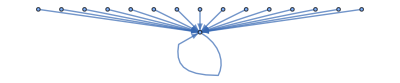
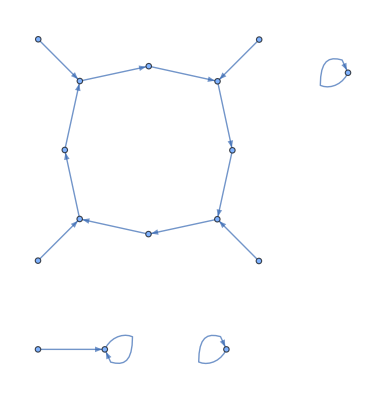
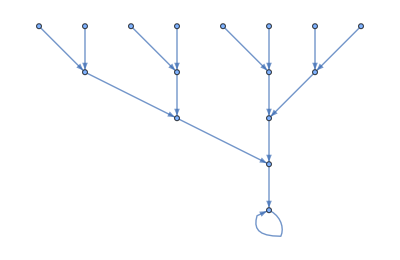
0_(2,3) | 30_(2,3) | 60_(2,3)
-Graphics- | -Graphics- | -Graphics-

```mathematica
space=4;
inits=Tuples[{0,1},4];
r23=Subscript[#,2,3]&/@Range[0,255];
r23evos=evos[r23,space];
Grid[{r23evos[[1;;80;;30,1]],r23evos[[1;;80;;30,2]]},Frame->All]
```

Si queremos comparar los grafos tenemos un problema, y es que aunque puedan tener la misma forma, los grafos no tienen las mismas transición, por ejemplo los siguientes 2:

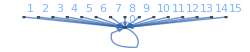
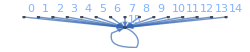
0_(2,3) | 255_(2,3)
-Graphics- | -Graphics-

```mathematica
Grid[Transpose[Table[{r23[[i]],GraphPlot[r23evos[[i,2]],VertexLabels->"Name",ImageSize->250]},{i,{1,-1}}]],Frame->All]
```

Para esto, vamos comparar si son isomorficos, es decir. Existe una funciṕon biyectiva que mapea los vertices de G y los vertices H del tal forma que su matriz de transición se conserva. Utilizamos la función nativa de Wolfram, comprobando que son isomorficos:

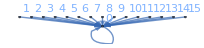
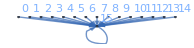
```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

True

Para saber si dos grafos son isomorficos, podemos obtener la forma canonica, si dos formas canonicas son iguales, entonces lso grafos son isomorficos.

Pero primero, utilizamos la siguiente función que optimiza la generación de estos grafos, guardandolos como una sola lista y no como una matriz:

```mathematica
TransMap[Subscript[n_,2,3],space_]:=Module[{tbl,configs,idx},tbl=IntegerDigits[n,2,8];(*tabla:vecindad 7,6,...,0*)configs=IntegerDigits[Range[0,2^space-1],2,space];
idx=4 (RotateRight/@configs)+2 configs+(RotateLeft/@configs);
(*sucesor de la config i (como entero,1-indexado)*)Map[FromDigits[#,2]&,Map[tbl[[8-#]]&,idx,{2}]]+1]
```

Despues, usamos la siguiente función para obtener la forma canonica de cada grafo:

```mathematica
CanonFuncGraph[f_List]:=Module[{n=Length[f],indeg,preds,code,queue,visited,cycles},indeg=ConstantArray[0,n];
Do[indeg[[f[[i]]]]++,{i,n}];
preds=ConstantArray[{},n];
code=ConstantArray[Null,n];
(*codificación canónica de los árboles,pelando hojas*)queue=Flatten@Position[indeg,0];
While[queue=!={},With[{v=First[queue]},queue=Rest[queue];
code[[v]]={Sort[preds[[v]]]};
With[{w=f[[v]]},AppendTo[preds[[w]],code[[v]]];
If[--indeg[[w]]==0,AppendTo[queue,w]]]]];
(*los nodos con indeg>0 restante están en ciclos*)visited=ConstantArray[False,n];cycles={};
Do[If[indeg[[v]]>0&&!visited[[v]],Module[{c={},w=v},While[!visited[[w]],visited[[w]]=True;
AppendTo[c,w];w=f[[w]]];
AppendTo[cycles,c]]],{v,n}];
(*llave:por ciclo,rotación lexicográficamente mínima de los códigos*)Sort[Module[{seq=({Sort[preds[[#]]]}&/@#)},First@Sort@Table[RotateLeft[seq,j],{j,Length[seq]}]]&/@cycles]]
```

No existe una forma absoluta de obtener la forma canonica, el metodo que se esta utilizando es el siguiente:

Se calcula el grado de entrada de cada nodo y se encunetran los nodos hoja.

Encolar los nodos hoja y por cada nodo hoja:

Buscar en el padre y asignarle un “codigo” de estructura, si al eliminar el nodo hoja el padre se vuelve un nodo hoja, tambien se encola.

Se buscan los ciclos y se nombra según la minima combinación.

Ahora, definimos los grafos para todas las r23:

```mathematica
r23f=ParallelMap[TransMap[#,4]&,r23];
gr23s4=Values[GroupBy[Transpose[{r23,r23f}],CanonFuncGraph@*Last->First]];
gr23s4[[;;10]]
```

{{0_(2,3),255_(2,3)},{1_(2,3),127_(2,3)},{2_(2,3),16_(2,3),191_(2,3),247_(2,3)},{3_(2,3),17_(2,3),63_(2,3),119_(2,3)},{4_(2,3),223_(2,3)},{5_(2,3),95_(2,3)},{6_(2,3),20_(2,3),159_(2,3),215_(2,3)},{7_(2,3),21_(2,3),31_(2,3),87_(2,3)},{8_(2,3),64_(2,3),239_(2,3),253_(2,3)},{9_(2,3),65_(2,3),111_(2,3),125_(2,3)}}

Estas son las reglas agrupadas en función de sus expresiones canonicas. Y estas son las agrupaciones con los resultados anteriormente obtenidos:

```mathematica
wkr23=;
wkr23[[;;10]]
```

{{0_(2,3),255_(2,3)},{1_(2,3),127_(2,3)},{2_(2,3),191_(2,3),16_(2,3),247_(2,3)},{3_(2,3),63_(2,3),17_(2,3),119_(2,3)},{5_(2,3),95_(2,3)},{14_(2,3),143_(2,3),84_(2,3),213_(2,3)},{15_(2,3),85_(2,3)},{18_(2,3),183_(2,3)},{23_(2,3)},{28_(2,3),199_(2,3),70_(2,3),157_(2,3)}}

Sin embargo, no son exactamente iguales:

```mathematica
wkr23==gr23s4
```

False

Pero las agrupaciones hechas por gr23s4, contienen agrupaciones completas hechas por los metodos ya investigados:

```mathematica
Grid[Select[Table[{g,Select[wkr23,SubsetQ[g,#]&]},{g,gr23s4}],Length[#[[2]]]>1&],Frame->All]
```

{15_(2,3),85_(2,3),170_(2,3),240_(2,3)} | {{15_(2,3),85_(2,3)},{240_(2,3),170_(2,3)}}
{23_(2,3),178_(2,3)} | {{23_(2,3)},{178_(2,3)}}
{25_(2,3),45_(2,3),61_(2,3),67_(2,3),75_(2,3),89_(2,3),101_(2,3),103_(2,3)} | {{45_(2,3),75_(2,3),101_(2,3),89_(2,3)},{67_(2,3),61_(2,3),25_(2,3),103_(2,3)}}
{28_(2,3),70_(2,3),78_(2,3),92_(2,3),141_(2,3),157_(2,3),197_(2,3),199_(2,3)} | {{28_(2,3),199_(2,3),70_(2,3),157_(2,3)},{78_(2,3),141_(2,3),92_(2,3),197_(2,3)}}
{77_(2,3),232_(2,3)} | {{77_(2,3)},{232_(2,3)}}
{105_(2,3),150_(2,3)} | {{105_(2,3)},{150_(2,3)}}

Esto quiere decir, que las agrupaciones de espejo y permutacion de estados dan como resultado los mismos grafos isomorficos. Y que adicionalmente, dependiendiendo de la configuración inicial, esos grafos puede tener similitud con otras reglas, al menos en el patrón de evoluciones.

¿Si podemos representar a la evolución como un grafo surge una pregunta muy importante. De que tamaño tiene que ser el espacio?

```mathematica
gr23s=Module[{r23f,gr23s},
r23f=Table[ParallelMap[TransMap[#,i]&,r23],{i,1,12}];
ParallelTable[
gr23s=Values[GroupBy[Transpose[{r23,i}],CanonFuncGraph@*Last->First]]
,{i,r23f}]
];
```

{0_(2,3),1_(2,3),128_(2,3)}

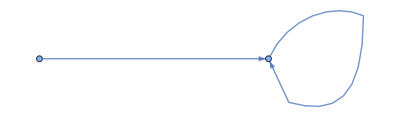
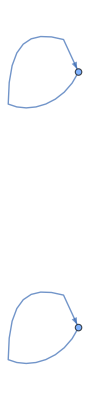
0_(2,3) | 1_(2,3) | 128_(2,3)
-Graphics- | -Graphics- | -Graphics-

```mathematica
gr23s[[1,;;,1]]
Grid[{evos[{Subscript[0, 2,3],Subscript[1, 2,3],Subscript[128, 2,3]},1][[;;,1]],evos[{Subscript[0, 2,3],Subscript[1, 2,3],Subscript[128, 2,3]},1][[;;,2]]},Frame->All]
```

```mathematica
ListLinePlot[Labeled[Length[#],Length[#]]&/@gr23s,InterpolationOrder->0,Mesh->Full,Filling->Bottom,PlotRange->All,AxesLabel->{"neighbourhood size", "unique behaviours"},ImageSize->Large]
```

-Graphics-

Es a partir de un tamaño de 4 que observamos un estancamiento en el descubrimiento de nuevos patrones. Lo mas cercano son 85 de las 88 agrupaciones ya conocidas. A conitnuación exploramos como es que estas reglas se estan asociando bajo dfeirentes tamaños de espacio:

```mathematica
diffr23=Table[
Select[Table[Select[wkr23,SubsetQ[g,#]&],{g,gr}],Length[#]>1&],{gr,gr23s}
][[4;;]];
Grid[Transpose[{diffr23}],Frame->All]
```

{{{15_(2,3),85_(2,3)},{240_(2,3),170_(2,3)}},{{23_(2,3)},{178_(2,3)}},{{45_(2,3),75_(2,3),101_(2,3),89_(2,3)},{67_(2,3),61_(2,3),25_(2,3),103_(2,3)}},{{28_(2,3),199_(2,3),70_(2,3),157_(2,3)},{78_(2,3),141_(2,3),92_(2,3),197_(2,3)}},{{77_(2,3)},{232_(2,3)}},{{105_(2,3)},{150_(2,3)}}}
{{{48_(2,3),243_(2,3),34_(2,3),187_(2,3)},{175_(2,3),10_(2,3),245_(2,3),80_(2,3)}},{{46_(2,3),139_(2,3),116_(2,3),209_(2,3)},{66_(2,3),189_(2,3),24_(2,3),231_(2,3)}},{{28_(2,3),199_(2,3),70_(2,3),157_(2,3)},{161_(2,3),122_(2,3)}},{{36_(2,3),219_(2,3)},{72_(2,3),237_(2,3)}},{{78_(2,3),141_(2,3),92_(2,3),197_(2,3)},{203_(2,3),44_(2,3),217_(2,3),100_(2,3)}},{{250_(2,3),160_(2,3)},{252_(2,3),192_(2,3),238_(2,3),136_(2,3)}}}
{{{15_(2,3),85_(2,3)},{240_(2,3),170_(2,3)}},{{23_(2,3)},{178_(2,3)}},{{77_(2,3)},{232_(2,3)}}}
{{{48_(2,3),243_(2,3),34_(2,3),187_(2,3)},{175_(2,3),10_(2,3),245_(2,3),80_(2,3)}},{{15_(2,3),85_(2,3)},{105_(2,3)}},{{46_(2,3),139_(2,3),116_(2,3),209_(2,3)},{66_(2,3),189_(2,3),24_(2,3),231_(2,3)}},{{90_(2,3),165_(2,3)},{153_(2,3),102_(2,3),195_(2,3),60_(2,3)}},{{250_(2,3),160_(2,3)},{252_(2,3),192_(2,3),238_(2,3),136_(2,3)}},{{150_(2,3)},{240_(2,3),170_(2,3)}}}
{{{15_(2,3),85_(2,3)},{240_(2,3),170_(2,3)}},{{23_(2,3)},{178_(2,3)}},{{77_(2,3)},{232_(2,3)}},{{105_(2,3)},{150_(2,3)}}}
{{{48_(2,3),243_(2,3),34_(2,3),187_(2,3)},{175_(2,3),10_(2,3),245_(2,3),80_(2,3)}},{{46_(2,3),139_(2,3),116_(2,3),209_(2,3)},{66_(2,3),189_(2,3),24_(2,3),231_(2,3)}},{{250_(2,3),160_(2,3)},{252_(2,3),192_(2,3),238_(2,3),136_(2,3)}}}
{{{15_(2,3),85_(2,3)},{240_(2,3),170_(2,3)}},{{23_(2,3)},{178_(2,3)}},{{77_(2,3)},{232_(2,3)}}}
{{{48_(2,3),243_(2,3),34_(2,3),187_(2,3)},{175_(2,3),10_(2,3),245_(2,3),80_(2,3)}},{{46_(2,3),139_(2,3),116_(2,3),209_(2,3)},{66_(2,3),189_(2,3),24_(2,3),231_(2,3)}},{{250_(2,3),160_(2,3)},{252_(2,3),192_(2,3),238_(2,3),136_(2,3)}}}
{{{15_(2,3),85_(2,3)},{240_(2,3),170_(2,3)}},{{23_(2,3)},{178_(2,3)}},{{77_(2,3)},{232_(2,3)}},{{105_(2,3)},{150_(2,3)}}}

Estos son las relaciones que se estan encontrado segun el comportamiento si incrementamos el tamaño, lo que involucra unas 24 reglas en total:

```mathematica
pairs=DeleteDuplicates[Flatten[diffr23[[;;,;;,;;,1]],1]]
DeleteDuplicates[Flatten[pairs]]
```

{{15_(2,3),240_(2,3)},{23_(2,3),178_(2,3)},{45_(2,3),67_(2,3)},{28_(2,3),78_(2,3)},{77_(2,3),232_(2,3)},{105_(2,3),150_(2,3)},{48_(2,3),175_(2,3)},{46_(2,3),66_(2,3)},{28_(2,3),161_(2,3)},{36_(2,3),72_(2,3)},{78_(2,3),203_(2,3)},{250_(2,3),252_(2,3)},{15_(2,3),105_(2,3)},{90_(2,3),153_(2,3)},{150_(2,3),240_(2,3)}}

{15_(2,3),240_(2,3),23_(2,3),178_(2,3),45_(2,3),67_(2,3),28_(2,3),78_(2,3),77_(2,3),232_(2,3),105_(2,3),150_(2,3),48_(2,3),175_(2,3),46_(2,3),66_(2,3),161_(2,3),36_(2,3),72_(2,3),203_(2,3),250_(2,3),252_(2,3),90_(2,3),153_(2,3)}

Podemos obtener una distancia calculando los valores propios de la matriz de transición de cada grafo y utilizar la distancia coseno para medir la diferencia entre dichas regalas:

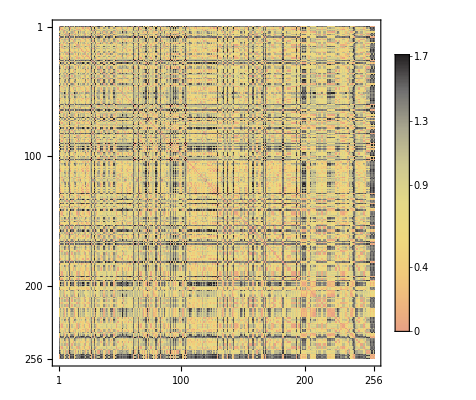

```mathematica
vecs=Table[
a=TransMap[r,4];
m=ConstantArray[0,{Length[a],Length[a]}];
Do[
m[[i,a[[i]]]]=1;
,{i,Length[a]}
];
Eigenvalues[m],
{r,r23}];
distances=DistanceMatrix[vecs,DistanceFunction->CosineDistance];
MatrixPlot[distances,ColorFunction->"CMYKColors",PlotLegends->Automatic]
```

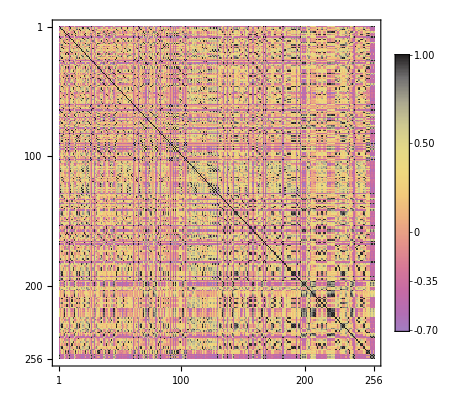

O podemos verlo unicamente en los comportamientos unicos obtenidos con gr23s4:

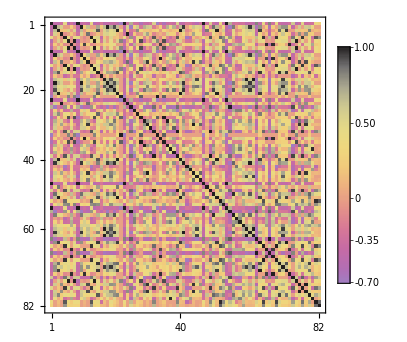

```mathematica
vecs=Table[
a=TransMap[r,4];
m=ConstantArray[0,{Length[a],Length[a]}];
Do[
m[[i,a[[i]]]]=1;
,{i,Length[a]}
];
Eigenvalues[m],
{r,gr23s4[[;;,1]]}];

distances=1-DistanceMatrix[vecs,DistanceFunction->CosineDistance];
MatrixPlot[distances,ColorFunction->"CMYKColors",PlotLegends->Automatic]
```

```mathematica
distances[[#[[1,1]]+1,#[[2,1]]+1]]&/@Tuples[#,2]&/@wkr23[[;;]]
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1},{1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1},{1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1}}

```mathematica
Extract[distances,#+1]&/@#[[1]]&/@gr23s4
```